```mathematica
data=Import["/Users/jaimebuitrago/Dropbox/Jaime/WolframCode/world-bank-data-1960-to-2016/country_population.csv"]
```

{1}
 |  |  |  |

```mathematica
data[[1,All]]
```

{Country Name,Country Code,Indicator Name,Indicator Code,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016}

```mathematica
dataset=Dataset@data
```

Dataset[<>]

```mathematica
dataset[[1;;5]]
```

Dataset[<>]

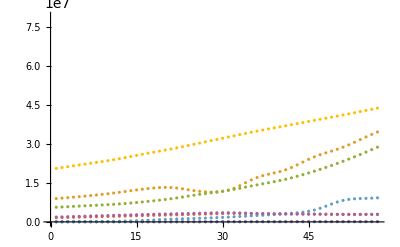

```mathematica
ListPlot@dataset[2;;10,5;;]
```